# Wahadło podwójne

```mathematica
R1[t_] = {L1 Sin[θ1[t]], -L1 Cos[θ1[t]]};
R2[t_] = {L2 Sin[θ2[t]], -L2 Cos[θ2[t]]} +R1[t];
```

```mathematica
F1[t_] = {0, -m1 g} - T1[t]/L1 R1[t] + T2[t]/L2 (R2[t] - R1[t]);
F2[t_] = {0, -m2 g} + T2[t]/L2 (R1[t] - R2[t]);
```

```mathematica
eq1 = m1 R1''[t] - F1[t]
```

{Sin[θ1[t]] T1[t]-Sin[θ2[t]] T2[t]+m1 (-L1 Sin[θ1[t]] θ1'[t]^2+L1 Cos[θ1[t]] θ1''[t]),g m1-Cos[θ1[t]] T1[t]+Cos[θ2[t]] T2[t]+m1 (L1 Cos[θ1[t]] θ1'[t]^2+L1 Sin[θ1[t]] θ1''[t])}

```mathematica
eq2 = m2 R2''[t] - F2[t]
```

{Sin[θ2[t]] T2[t]+m2 (-L1 Sin[θ1[t]] θ1'[t]^2-L2 Sin[θ2[t]] θ2'[t]^2+L1 Cos[θ1[t]] θ1''[t]+L2 Cos[θ2[t]] θ2''[t]),g m2-Cos[θ2[t]] T2[t]+m2 (L1 Cos[θ1[t]] θ1'[t]^2+L2 Cos[θ2[t]] θ2'[t]^2+L1 Sin[θ1[t]] θ1''[t]+L2 Sin[θ2[t]] θ2''[t])}

```mathematica
FQ1 =TrigReduce[ eq1[[1]] Cos[θ1[t]] + eq1[[2]] Sin[θ1[t]] + eq2[[1]] Cos[θ1[t]] + eq2[[2]] Sin[θ1[t]]]/.{θ1'[t] -> ω1[t], θ2'[t] ->ω2[t],  θ1''[t] ->ω1'[t], θ2''[t] ->ω2'[t]}
```

g m1 Sin[θ1[t]]+g m2 Sin[θ1[t]]+L2 m2 Sin[θ1[t]-θ2[t]] ω2[t]^2+L1 m1 ω1'[t]+L1 m2 ω1'[t]+L2 m2 Cos[θ1[t]-θ2[t]] ω2'[t]

```mathematica
FQ2 = TrigReduce[eq2[[1]] Cos[θ2[t]] + eq2[[2]] Sin[θ2[t]]]/. {θ1'[t] -> ω1[t],
 θ2'[t] ->ω2[t],  θ1''[t] ->ω1'[t], θ2''[t] ->ω2'[t]}
```

g m2 Sin[θ2[t]]-L1 m2 Sin[θ1[t]-θ2[t]] ω1[t]^2+L1 m2 Cos[θ1[t]-θ2[t]] ω1'[t]+L2 m2 ω2'[t]

```mathematica
g = 9.81; L1 =5; L2=3; m1=1; m2=1;
sol=NDSolve[{FQ1 == 0, FQ2 == 0, θ1'[t] == ω1[t], θ2'[t] == ω2[t], θ1[0] == π/6, θ2[0] == π/3,ω1[0] == 0, ω2[0] == 0},
{θ1[t],θ2[t], ω1[t], ω2[t]}, {t,0,20}]
```

{{θ1[t]→InterpolatingFunction[{{0.,20.}},<>][t],θ2[t]→InterpolatingFunction[{{0.,20.}},<>][t],ω1[t]→InterpolatingFunction[{{0.,20.}},<>][t],ω2[t]→InterpolatingFunction[{{0.,20.}},<>][t]}}

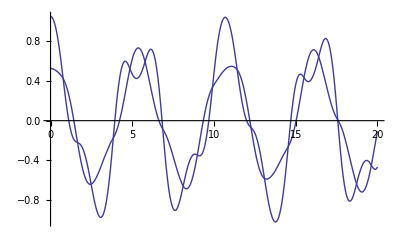

```mathematica
Plot[{θ1[t], θ2[t]}/. First@sol, {t,0,20}]
```

```mathematica
r1[t_] = {L1 Sin[θ1[t]], -L1 Cos[θ1[t]]}/.First@sol
```

{5 Sin[InterpolatingFunction[{{0.,20.}},<>][t]],-5 Cos[InterpolatingFunction[{{0.,20.}},<>][t]]}

```mathematica
r2[t_] = {L2 Sin[θ2[t]], -L2 Cos[θ2[t]]} +r1[t]/.First@sol
```

{5 Sin[InterpolatingFunction[{{0.,20.}},<>][t]]+3 Sin[InterpolatingFunction[{{0.,20.}},<>][t]],-5 Cos[InterpolatingFunction[{{0.,20.}},<>][t]]-3 Cos[InterpolatingFunction[{{0.,20.}},<>][t]]}

```mathematica
Manipulate[Show[
Graphics[{Gray,Rectangle[{-1,0}, {1,1}]}],
Graphics[{Black,Thick, Line[{{-1,0},{1,0}}]}],
Graphics[{Black,Dashed, Line[{{0,0},{0,-L1 -L2 -2}}]}],
Graphics[{Orange, Line[{{0,0}, r1[T]}]}],
Graphics[{Orange, Line[{r1[T], r2[T]}]}],
Graphics[{Red, PointSize[0.03], Point[r1[T]]}],
Graphics[{Red, PointSize[0.03], Point[r2[T]]}],
ParametricPlot[r2[t], {t,0,T}, PlotStyle->Directive[Green, Thick]],
PlotRange -> {{-L1 - L2, L1 +L2}, {-L1 -L2 -2,1}}
], {T, 0.001, 20, AnimationRate->1}
]
```